{7→1,2→7,1→3,9→7,6→9,9→2,7→6,3→8,8→5,4→3,7→4,3→1,3→8,9→5,8→1}

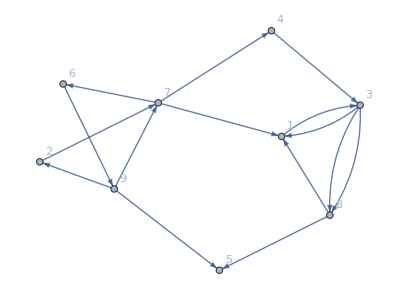

```mathematica
(* Determining whether there is a path in a directed graph. Quoted from <<Mathematica Cookbook>> *)

(* the number of vertex of a random graph. *)
n=10;

(* generating the graph randomly. *)
vertex=Range[n];
graph=Table[(tt=RandomChoice[vertex])->RandomChoice[Complement[vertex,{tt}]],{Floor[3n/2]}]

(* plot the graph *)
GraphPlot[graph,VertexLabels->Automatic,DirectedEdges->True]
```

```mathematica
(* idea: at every step, find new path, add it to the original graph, then next,  *)
(* when there is no new path found, check whether from->to is in the final graph. *)

hasPath[graph_,from_,from_]:=True
hasPath[graph_,from_,to_]:=Module[{graphTmp=graph},MemberQ[FixedPoint[(graphTmp=ReplaceAll[#,{a___,from->x_,b___,x_->y_,c___}|{a___,x_->y_,b___,from->x_,c___}/;Not@MemberQ[graphTmp,from->y]:>{from->y,x->y,from->x,a,b,c}])&,graphTmp],from->to]]
```

```mathematica
(* test the results. *)
Table[Boole[hasPath[graph,i,j]],{i,n},{j,n}]//MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)